```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Needs["ErrorBarPlots`"];
```

```mathematica
(*calculate I0 at different fractions fD2O*)
```

```mathematica
fD2O=1(*%*);
c=11.9(*mg mL^-1*);
NA=6.02214 10^23(*mol^-1*);
m1=29.267+0.435 fD2O(*kDa*);
m2=16.413+0.235 fD2O(*kDa*);
Δρ1=(2.495-5.589 fD2O)10^10 (*cm^-2*);
Δρ2=(6.230-5.567 fD2O)10^10 (*cm^-2*);
v1=0.732(*cm^3 g^-1*);
v2=0.724(*cm^3 g^-1*);
Mw=m1+m2;f1=m1 Mw^-1;f2=m2 Mw^-1;
I0=c Mw/NA (f1 Δρ1 v1+f2 Δρ2 v2)^2
```

0.149808

```mathematica
(*summarize the results of I0 in a single list*)
```

```mathematica
I0={0.7030,0.5137,0.3538,0.2745,0.020,0.0695,0.1498};
(*errors are considered proportional to the ones for Kin+2Sda complex*)
err0=0.7030/0.5212{0.0032,0.0026,0.0024,0.0014,0.0013,0.0014,0.0009};
c={11.9,11.9,11.9,26.6,11.9,11.9,11.9};
```

```mathematica
(*Calculate the ratio I(0)/c at every fraction fD2O, in units of cm^2 g^-1*)
```

```mathematica
I0c={{0,10^3/c⟦1⟧I0⟦1⟧},{10,10^3/c⟦2⟧I0⟦2⟧},{20,10^3/c⟦3⟧I0⟦3⟧},{40,10^3/c⟦4⟧I0⟦4⟧},{80,10^3/c⟦5⟧I0⟦5⟧},{90,10^3/c⟦6⟧I0⟦6⟧},{100,10^3/c⟦7⟧I0⟦7⟧}};
```

```mathematica
errratio=0.7030/0.5212{0.2689,0.2185,0.2016,0.1176,0.1092,0.1176,0.0756};
```

```mathematica
pts={{I0c⟦1⟧,ErrorBar[errratio⟦1⟧]},{I0c⟦2⟧,ErrorBar[errratio⟦2⟧]},{I0c⟦3⟧,ErrorBar[errratio⟦3⟧]},{I0c⟦4⟧,ErrorBar[errratio⟦4⟧]},{I0c⟦5⟧,ErrorBar[errratio⟦5⟧]},{I0c⟦6⟧,ErrorBar[errratio⟦6⟧]},{I0c⟦7⟧,ErrorBar[errratio⟦7⟧]}};
```

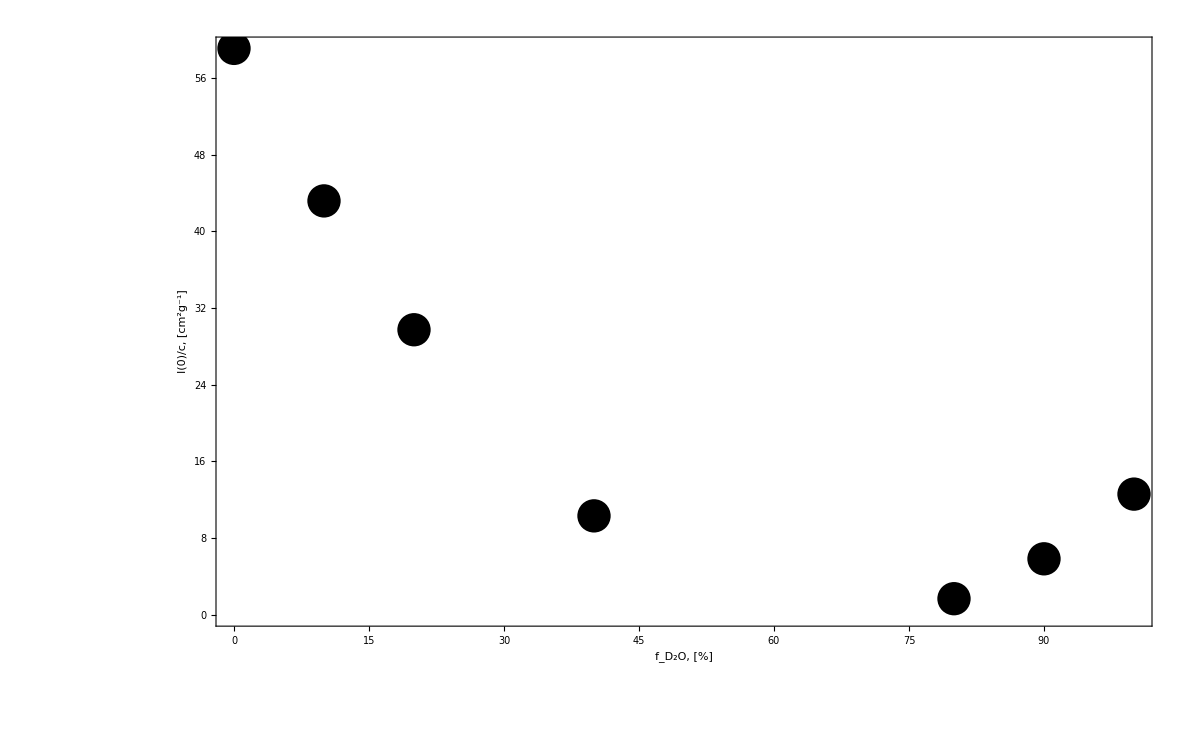

```mathematica
pointswitherrors=ErrorListPlot[pts,PlotStyle->{Black,PointSize[0.02],Thickness[.005]},Epilog->Inset[Style["k",56,Bold],{-10.9,45.5}],Axes->False,Frame->{{True,False},{True,False}},BaseStyle->{FontFamily->"Times New Roman",20},FrameStyle->Directive[Black,48,Thick],FrameLabel->{Row[{Subscript[Style["f",FontSlant->Italic], "D_2O"],", [%]"}],Row[{Style["I(0)/c",FontSlant->Italic], ", [cm^2g^-1]"}]},(*PlotRangeClipping->False,*)ImageSize->{1200,1200}]
```

```mathematica
nlm=NonlinearModelFit[pts⟦;;,1⟧,e+f x+g x^2,{e,f,g},x,Weights->1/errratio]
```

FittedModel[59.1455-1.72489 x+0.0125895 x^2]

```mathematica
(*find minimum*)
```

```mathematica
x/.Last[FindMinimum[nlm[x],{x,.5}]]
```

68.5054

```mathematica
nlm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
e | 59.1455 | 0.0567886 | 1041.5 | 5.09927×10^-12
f | -1.72489 | 0.0027945 | -617.246 | 4.13342×10^-11
g | 0.0125895 | 0.0000252854 | 497.894 | 9.76319×10^-11

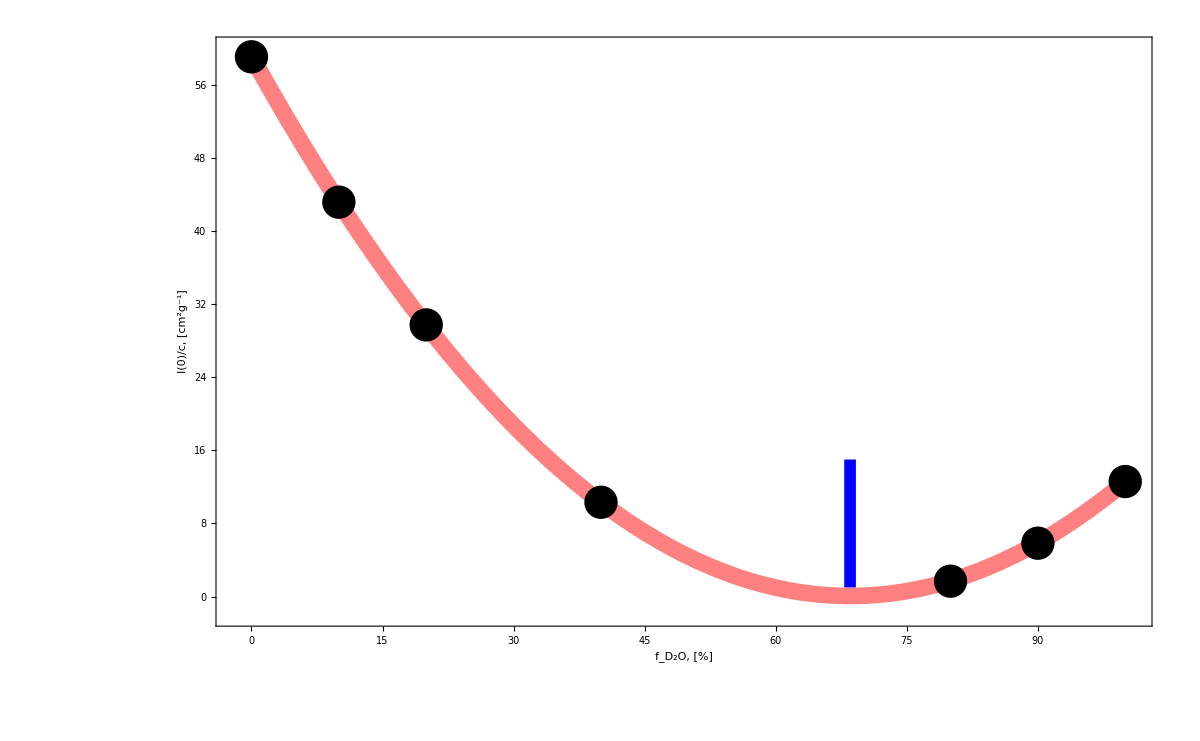

```mathematica
plt=Show[Plot[nlm[x],{x,0,100},PlotStyle->{Pink,Thickness[0.01]},PlotRange->{{-2,101},{-2,60}},Epilog->Inset[Style["k",56,Bold],{-12.9,61.1}],Axes->False,Frame->{{True,False},{True,False}},BaseStyle->{FontFamily->"Times New Roman",20},FrameStyle->Directive[Black,54,Thick],FrameLabel->{Row[{Subscript[Style["f",FontSlant->Italic],"D_2O"] ,", [%]"}],Row[{Style["I(0)/c",FontSlant->Italic], ", [cm^2g^-1]"}]},PlotRangeClipping->False,ImageSize->1200],pointswitherrors,Graphics[{Thickness[0.007],Blue,Arrow[{{x/.Last[FindMinimum[nlm[x],{x,.5}]],15},{x/.Last[FindMinimum[nlm[x],{x,.5}]],1}}]}]]
```

```mathematica
Export["fig6k.png",plt]
```

fig6k.png